## Microbiome-pathogen interactions drive epidemiological dynamics of antibiotic resistance: modelling insights for infection control

David R. M. Smith (david.smith@pasteur.fr); Laura Temime, Lulla Opatowski

## notes

- this notebook corresponds to the article of the same name
- models and their assumptions are described in the manuscript and supplementary file
- ODE solutions are limited to 0 ≤ S ≤ 1 for all state variables S
- notation varies slightly to manuscript: 
--- X denotes pathogen-colonized patients (C is protected)
--- N=1 in all models, drops from all equations
--- prime notation is not possible, instead parameter symbols are doubled (e.g. α’ --> αα)

## susceptible-colonized model

```mathematica
Remove["Global`*"]
```

### assumptions

#### acquisition

```mathematica
λ=β X;
α=αα(1-a(1-Subscript[r, R]));
```

#### fitness costs of resistance

```mathematica
γ=γγ (1+c);
```

#### antibiotics

```mathematica
Subscript[σ, X]=a(1-Subscript[r, R])Subscript[θ, X];
```

### ODEs

```mathematica
dS = (1-Subscript[f, X] Subscript[f, R])μ-S(λ+α+μ)+X(γ+Subscript[σ, X]);
dX =  Subscript[f, X] Subscript[f, R] μ+S(λ+α)-X(γ+Subscript[σ, X]+μ);
```

### parameter values

```mathematica
(*excludes a and r, as we evaluate over these*)
```

```mathematica
paramsSX = {
β->0.2,αα->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[θ, X]->0.2};
```

### prevalence

#### evaluated for a ∈ {0,1}, r = 0.8

```mathematica
eqba=Table[Flatten[{a,{S,X}/.NSolve[{dS==0,dX==0,0≤S≤1,0≤X≤1}/.paramsSX/.{Subscript[r, R]->0.8},{S,X}]}],{a,0,1,0.01}];
```

```mathematica
prevalenceX=eqba[[All,{1,3}]];
```

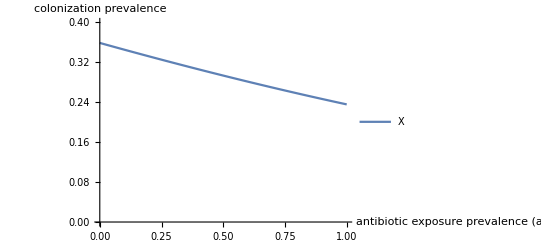

```mathematica
ListLinePlot[prevalenceX, PlotLegends->{X},AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence"},PlotRange->{0,0.4}]
```

#### evaluated for a ∈ {0,1}, r = 1

```mathematica
eqba=Table[Flatten[{a,{S,X}/.NSolve[{dS==0,dX==0,0≤S≤1,0≤X≤1}/.paramsSX/.{Subscript[r, R]->1},{S,X}]}],{a,0,1,0.01}];
```

```mathematica
prevalenceX=eqba[[All,{1,3}]];
```

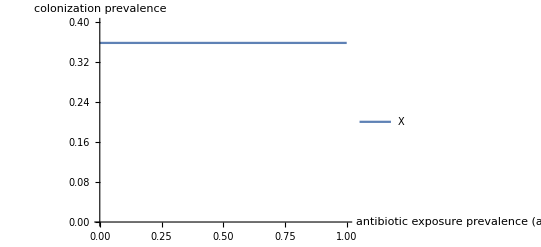

```mathematica
ListLinePlot[prevalenceX, PlotLegends->{X},AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence"},PlotRange->{0,0.4}]
```

### R_0

```mathematica
R0=(β+α)/(γ+Subscript[σ, X]+μ);
```

#### evaluate for a ∈ {0,1}, r ∈ {0,1}

```mathematica
R0eval=Flatten[Table[{a,Subscript[r, R],R0/.paramsSX},{a,0,1,0.01},{Subscript[r, R],0,1,0.01}],1];
```

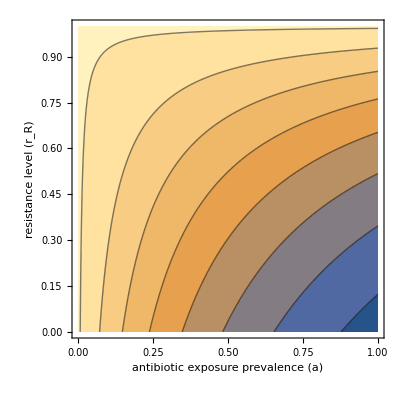

```mathematica
ListContourPlot[R0eval, FrameLabel->{"antibiotic exposure prevalence (a)", "resistance level (r_R)"}]
```

## exclusive colonization strain competition

```mathematica
Remove["Global`*"]
```

### assumptions

#### acquisition

```mathematica
(*dynamic transmission*)
```

```mathematica
Subscript[λ, S]=β Subscript[X, S]; 
Subscript[λ, R]=β Subscript[X, R];
```

```mathematica
(*endogenous acquisition only among patients not exposed to effective antibiotic therapy*)
```

```mathematica
Subscript[α, S]=Subscript[αα, S](1-a(1-Subscript[r, S]));
Subscript[α, R]=Subscript[αα, R](1-a(1-Subscript[r, R]));
```

#### fitness costs of resistance

```mathematica
Subscript[γ, S]=γγ ;
Subscript[γ, R]=γγ (1+c);
```

#### antibiotics

```mathematica
Subscript[σ, S]=a(1-Subscript[r, S])Subscript[θ, X];
Subscript[σ, R]=a(1-Subscript[r, R])Subscript[θ, X];
```

### ODEs

#### baseline

```mathematica
dS = (1-Subscript[f, X])μ-S(Subscript[λ, S]+Subscript[λ, R]+Subscript[α, S]+Subscript[α, R]+μ)+Subscript[X, S](Subscript[γ, S]+Subscript[σ, S])+Subscript[X, R](Subscript[γ, R]+Subscript[σ, R]);
Subscript[dX, S] =  Subscript[f, X](1-Subscript[f, R]) μ+S(Subscript[λ, S]+Subscript[α, S])-Subscript[X, S](Subscript[γ, S]+Subscript[σ, S]+μ);
Subscript[dX, R] =  Subscript[f, X] Subscript[f, R] μ+S(Subscript[λ, R]+Subscript[α, R])-Subscript[X, R](Subscript[γ, R]+Subscript[σ, R]+μ);
```

### parameter values

```mathematica
(*excludes a and Subscript[r, R], as we evaluate over these*)
```

#### parameters in absence of X_R (to evaluate at disease-free equilibrium, DFE) reflecting endemic X_R

```mathematica
paramsStrainCompNoXR = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0,γγ->0.03,c->0,
μ->0.1,Subscript[f, X]->0.1,Subscript[f, R]->0,Subscript[θ, X]->0.2,Subscript[r, S]->0};
```

#### parameters given invading X_R

```mathematica
paramsStrainComp = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, X]->0.1,Subscript[f, R]->0.5,
Subscript[θ, X]->0.2,Subscript[r, S]->0};
```

### prevalence

#### evaluated for a ∈ {0,1}, r_R = 0.8

```mathematica
eqba=Table[Flatten[{a,{S,Subscript[X, S],Subscript[X, R]}/.NSolve[{dS==0,Subscript[dX, S]==0, Subscript[dX, R]==0,0≤S≤1,0≤Subscript[X, S]≤1,0≤Subscript[X, R]≤1}/.paramsStrainComp/.{Subscript[r, R]->0.8},{S,Subscript[X, S],Subscript[X, R]}]}],{a,0,1,0.01}];
```

```mathematica
Subscript[prevalenceX, S]=eqba[[All,{1,3}]];
Subscript[prevalenceX, R]=eqba[[All,{1,4}]];
```

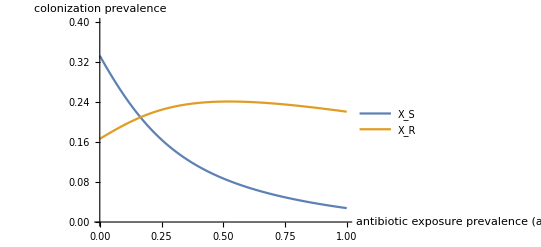

```mathematica
ListLinePlot[{Subscript[prevalenceX, S],Subscript[prevalenceX, R]}, PlotLegends->{Subscript[X, S],Subscript[X, R]},PlotRange->{0,0.4},AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence"}]
```

#### evaluated for a ∈ {0,1}, r_R = 1

```mathematica
eqba=Table[Flatten[{a,{S,Subscript[X, S],Subscript[X, R]}/.NSolve[{dS==0,Subscript[dX, S]==0, Subscript[dX, R]==0,0≤S≤1,0≤Subscript[X, S]≤1,0≤Subscript[X, R]≤1}/.paramsStrainComp/.{Subscript[r, R]->1},{S,Subscript[X, S],Subscript[X, R]}]}],{a,0,1,0.01}];
```

```mathematica
Subscript[prevalenceX, S]=eqba[[All,{1,3}]];
Subscript[prevalenceX, R]=eqba[[All,{1,4}]];
```

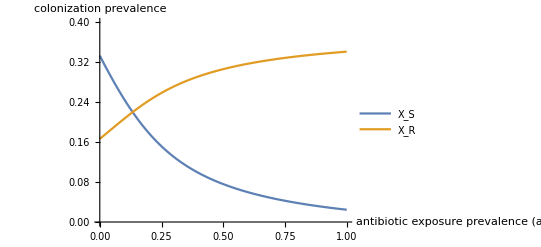

```mathematica
ListLinePlot[{Subscript[prevalenceX, S],Subscript[prevalenceX, R]}, PlotLegends->{Subscript[X, S],Subscript[X, R]},AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence"},PlotRange->{0,0.4}]
```

### R_0

```mathematica
R0=Subscript[S, DFE](β+Subscript[α, R])/(Subscript[γ, R]+Subscript[σ, R]+μ);
```

#### evaluate for a ∈ {0,1}, r ∈ {0,1}

```mathematica
(*function to select equilibrium value of S from solution*)
```

```mathematica
f[sol_]:=S/.sol[[1,1]]
```

```mathematica
R0eval=Table[{a,Subscript[r, R],R0/.paramsStrainComp/.Subscript[S, DFE]->f[NSolve[{dS==0,Subscript[dX, S]==0, Subscript[dX, R]==0,Subscript[X, R]==0,0≤S≤1,0≤Subscript[X, S]≤1}/.paramsStrainCompNoXR,{S,Subscript[X, S],Subscript[X, R]}]]},{a,0,1,0.01},{Subscript[r, R],0,1,0.01}];
```

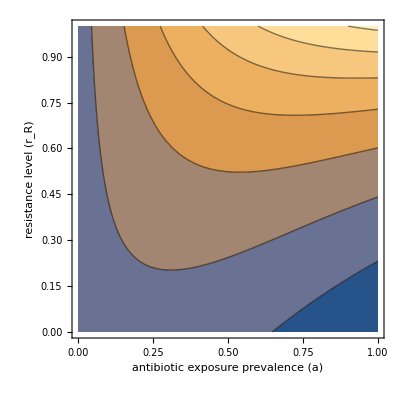

```mathematica
ListContourPlot[Flatten[R0eval,1], FrameLabel->{"antibiotic exposure prevalence (a)", "resistance level (r_R)"}]
```

## microbiome competition (1 strain)

```mathematica
Remove["Global`*"]
```

### assumptions

#### acquisition

```mathematica
λ=β (Subscript[X, e]+Subscript[X, d]);
Subscript[λ, ϵ]=(1-ϵ)β (Subscript[X, e]+Subscript[X, d]);
α=αα(1-a(1-Subscript[r, R]));
Subscript[α, ϕ]=ϕ αα(1-a(1-Subscript[r, R]));
```

#### fitness costs of resistance

```mathematica
γ=γγ (1+c);
Subscript[γ, η]=(1-η)γγ (1+c);
```

#### antibiotics

```mathematica
Subscript[σ, X]=a(1-Subscript[r, R])Subscript[θ, X];
Subscript[σ, m]=a Subscript[θ, m];
```

#### microbiome recovery

```mathematica
δ=δδ(1-a);
```

### ODEs

#### baseline

```mathematica
Subscript[dS, e] = (1-Subscript[f, X] Subscript[f, R])(1-Subscript[f, d])μ-Subscript[S, e](Subscript[λ, ϵ]+α+Subscript[σ, m]+μ)+Subscript[S, d] δ+Subscript[X, e](γ+Subscript[σ, X]);
Subscript[dS, d]=(1-Subscript[f, X Subscript[f, R]])Subscript[f, d] μ+Subscript[S, e] Subscript[σ, m]-Subscript[S, d](λ+Subscript[α, ϕ]+δ+μ)+Subscript[X, d](Subscript[γ, η]+Subscript[σ, X]);
Subscript[dX, e] =  Subscript[f, X] Subscript[f, R](1-Subscript[f, d]) μ+Subscript[S, e](Subscript[λ, ϵ]+α)-Subscript[X, e](γ+Subscript[σ, m]+Subscript[σ, X]+μ)+Subscript[X, d] δ;
Subscript[dX, d] =  Subscript[f, X] Subscript[f, R] Subscript[f, d] μ+Subscript[S, d](λ+Subscript[α, ϕ])+Subscript[X, e] Subscript[σ, m]-Subscript[X, d](Subscript[γ, η]+δ+Subscript[σ, X]+μ);
```

#### invasion

```mathematica
(*no pathogen input, endogenous acquisition depends on prevalence*)
```

```mathematica
Subscript[dS, eDFE] = (1-Subscript[f, d])μ-Subscript[S, e](Subscript[λ, ϵ]+α(Subscript[X, e]+Subscript[X, d])+Subscript[σ, m]+μ)+Subscript[S, d] δ+Subscript[X, e](γ+Subscript[σ, X]);
Subscript[dS, dDFE]=Subscript[f, d] μ+Subscript[S, e] Subscript[σ, m]-Subscript[S, d](λ+Subscript[α, ϕ](Subscript[X, e]+Subscript[X, d])+δ+μ)+Subscript[X, d](Subscript[γ, η]+Subscript[σ, X]);
Subscript[dX, eDFE] = Subscript[S, e](Subscript[λ, ϵ]+α*(Subscript[X, e]+Subscript[X, d]))-Subscript[X, e](γ+Subscript[σ, m]+Subscript[σ, X]+μ)+Subscript[X, d] δ;
Subscript[dX, dDFE] =  Subscript[S, d](λ+Subscript[α, ϕ]*(Subscript[X, e]+Subscript[X, d]))+Subscript[X, e] Subscript[σ, m]-Subscript[X, d](Subscript[γ, η]+δ+Subscript[σ, X]+μ);
```

### parameter values

```mathematica
(*excludes a and r, as we evaluate over these*)
```

#### consider three strengths of microbiome-pathogen interactions

```mathematica
paramsMicrobiome = {
β->0.2,αα->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, d]->0,
Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7
};
```

```mathematica
paramsMicrobiomeϵ1 = Flatten[Append[paramsMicrobiome,{ϵ->0.2,η->0,ϕ->1}]];
paramsMicrobiomeϵ2 = Flatten[Append[paramsMicrobiome,{ϵ->0.5,η->0,ϕ->1}]];
paramsMicrobiomeϵ3 = Flatten[Append[paramsMicrobiome,{ϵ->0.8,η->0,ϕ->1}]];
paramsMicrobiomeη1 = Flatten[Append[paramsMicrobiome,{ϵ->0,η->0.2,ϕ->1}]];
paramsMicrobiomeη2 = Flatten[Append[paramsMicrobiome,{ϵ->0,η->0.5,ϕ->1}]];
paramsMicrobiomeη3 = Flatten[Append[paramsMicrobiome,{ϵ->0,η->0.8,ϕ->1}]];
paramsMicrobiomeϕ1 = Flatten[Append[paramsMicrobiome,{ϵ->0,η->0,ϕ->2}]];
paramsMicrobiomeϕ2 = Flatten[Append[paramsMicrobiome,{ϵ->0,η->0,ϕ->5}]];
paramsMicrobiomeϕ3 = Flatten[Append[paramsMicrobiome,{ϵ->0,η->0,ϕ->8}]];
paramsMicrobiomeMixed = Flatten[Append[paramsMicrobiome,{ϵ->0.5,η->0.5,ϕ->5}]];
```

### prevalence

#### evaluated for a ∈ {0,1}, r_R = 0.8 for different interactions and interaction strengths

```mathematica
eqbaϵ1=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϵ1/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϵ2=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϵ2/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϵ3=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϵ3/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaη1=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeη1/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaη2=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeη2/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaη3=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeη3/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϕ1=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϕ1/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϕ2=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϕ2/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϕ3=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϕ3/.{Subscript[r, R]->0.8},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
```

```mathematica
prevalenceϵ1=Transpose[{eqbaϵ1[[All,1]],eqbaϵ1[[All,4]]+eqbaϵ1[[All,5]]}];prevalenceϵ2=Transpose[{eqbaϵ2[[All,1]],eqbaϵ2[[All,4]]+eqbaϵ2[[All,5]]}];prevalenceϵ3=Transpose[{eqbaϵ3[[All,1]],eqbaϵ3[[All,4]]+eqbaϵ3[[All,5]]}];
prevalenceη1=Transpose[{eqbaη1[[All,1]],eqbaη1[[All,4]]+eqbaη1[[All,5]]}];prevalenceη2=Transpose[{eqbaη2[[All,1]],eqbaη2[[All,4]]+eqbaη2[[All,5]]}];prevalenceη3=Transpose[{eqbaη3[[All,1]],eqbaη3[[All,4]]+eqbaη3[[All,5]]}];
prevalenceϕ1=Transpose[{eqbaϕ1[[All,1]],eqbaϕ1[[All,4]]+eqbaϕ1[[All,5]]}];prevalenceϕ2=Transpose[{eqbaϕ2[[All,1]],eqbaϕ2[[All,4]]+eqbaϕ2[[All,5]]}];prevalenceϕ3=Transpose[{eqbaϕ3[[All,1]],eqbaϕ3[[All,4]]+eqbaϕ3[[All,5]]}];
```

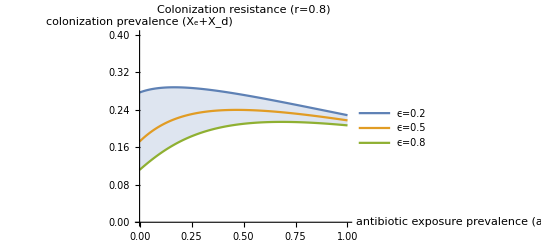

```mathematica
ListLinePlot[{prevalenceϵ1,prevalenceϵ2,prevalenceϵ3}, PlotLegends->{"ϵ=0.2","ϵ=0.5","ϵ=0.8"},PlotLabel->"Colonization resistance (r=0.8)",AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence (X_e+X_d)"},PlotRange->{0,0.4},Filling->{1->{3}}]
```

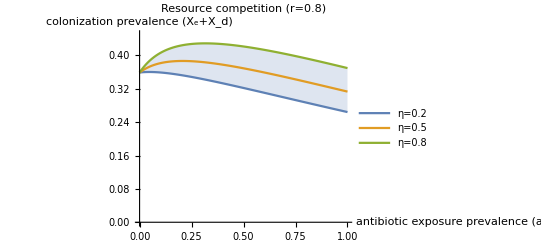

```mathematica
ListLinePlot[{prevalenceη1,prevalenceη2,prevalenceη3}, PlotLegends->{"η=0.2","η=0.5","η=0.8"},PlotLabel->"Resource competition (r=0.8)",AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence (X_e+X_d)"},PlotRange->{0,0.45},Filling->{1->{3}}]
```

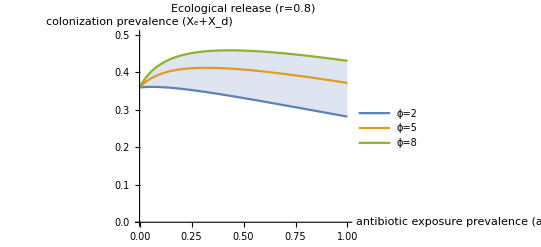

```mathematica
ListLinePlot[{prevalenceϕ1,prevalenceϕ2,prevalenceϕ3}, PlotLegends->{"ϕ=2","ϕ=5","ϕ=8"},PlotLabel->"Ecological release (r=0.8)",AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence (X_e+X_d)"},PlotRange->{0,0.5},Filling->{1->{3}}]
```

#### evaluated for a ∈ {0,1}, r_R = 1.0 for different interactions and interaction strengths

```mathematica
eqbaϵ1=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϵ1/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϵ2=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϵ2/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϵ3=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϵ3/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaη1=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeη1/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaη2=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeη2/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaη3=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeη3/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϕ1=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϕ1/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϕ2=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϕ2/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
eqbaϕ3=Table[Flatten[{a,{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}/.NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, e]==0, Subscript[dX, d]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, e]≤1,0≤Subscript[X, d]≤1}/.paramsMicrobiomeϕ3/.{Subscript[r, R]->1},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]}],{a,0,1,0.01}];
```

```mathematica
prevalenceϵ1=Transpose[{eqbaϵ1[[All,1]],eqbaϵ1[[All,4]]+eqbaϵ1[[All,5]]}];prevalenceϵ2=Transpose[{eqbaϵ2[[All,1]],eqbaϵ2[[All,4]]+eqbaϵ2[[All,5]]}];prevalenceϵ3=Transpose[{eqbaϵ3[[All,1]],eqbaϵ3[[All,4]]+eqbaϵ3[[All,5]]}];
prevalenceη1=Transpose[{eqbaη1[[All,1]],eqbaη1[[All,4]]+eqbaη1[[All,5]]}];prevalenceη2=Transpose[{eqbaη2[[All,1]],eqbaη2[[All,4]]+eqbaη2[[All,5]]}];prevalenceη3=Transpose[{eqbaη3[[All,1]],eqbaη3[[All,4]]+eqbaη3[[All,5]]}];
prevalenceϕ1=Transpose[{eqbaϕ1[[All,1]],eqbaϕ1[[All,4]]+eqbaϕ1[[All,5]]}];prevalenceϕ2=Transpose[{eqbaϕ2[[All,1]],eqbaϕ2[[All,4]]+eqbaϕ2[[All,5]]}];prevalenceϕ3=Transpose[{eqbaϕ3[[All,1]],eqbaϕ3[[All,4]]+eqbaϕ3[[All,5]]}];
```

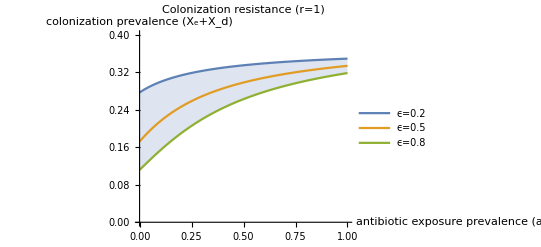

```mathematica
ListLinePlot[{prevalenceϵ1,prevalenceϵ2,prevalenceϵ3}, PlotLegends->{"ϵ=0.2","ϵ=0.5","ϵ=0.8"},PlotLabel->"Colonization resistance (r=1)",AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence (X_e+X_d)"},PlotRange->{0,0.4},Filling->{1->{3}}]
```

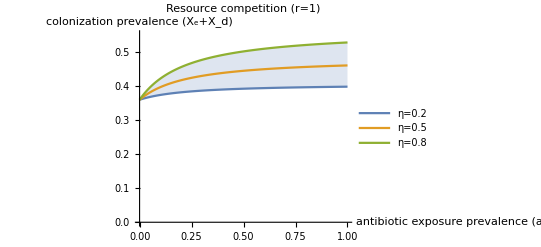

```mathematica
ListLinePlot[{prevalenceη1,prevalenceη2,prevalenceη3}, PlotLegends->{"η=0.2","η=0.5","η=0.8"},PlotLabel->"Resource competition (r=1)",AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence (X_e+X_d)"},PlotRange->{0,0.55},Filling->{1->{3}}]
```

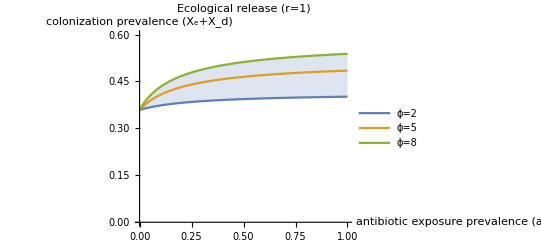

```mathematica
ListLinePlot[{prevalenceϕ1,prevalenceϕ2,prevalenceϕ3}, PlotLegends->{"ϕ=2","ϕ=5","ϕ=8"},PlotLabel->"Ecological release (r=1)",AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence (X_e+X_d)"},PlotRange->{0,0.6},Filling->{1->{3}}]
```

### R_0

#### NGM

```mathematica
F={{(α+(1-ϵ)β)Subscript[S, eDFE],(α+(1-ϵ)β)Subscript[S, eDFE]},{(α ϕ+β)Subscript[S, dDFE],(α ϕ+β)Subscript[S, dDFE]}};
V={{γ+Subscript[σ, X]+Subscript[σ, m]+μ, -δ},{-Subscript[σ, m],δ+(1-η)γ+Subscript[σ, X]+μ}};
NGM = F.Inverse[V];
R0=Total[Eigenvalues[NGM]];
R0//FullSimplify
```

((β+αα ϕ-a αα ϕ+a αα ϕ r_R) S_dDFE (γγ+c γγ+δδ-a δδ+μ+a θ_m-a (-1+r_R) θ_X)-(αα-a αα+β-β ϵ+a αα r_R) S_eDFE ((-1+a) δδ+(1+c) γγ (-1+η)-μ-a θ_m+a (-1+r_R) θ_X))/(-((-1+a) δδ+(1+c) γγ (-1+η)-μ+a (-1+r_R) θ_X) (γγ+c γγ+μ+(a-a r_R) θ_X)+a θ_m (-(1+c) γγ (-1+η)+μ+(a-a r_R) θ_X))

```mathematica
DFE=Flatten[Solve[{Subscript[dS, eDFE]==0,Subscript[dS, dDFE]==0,Subscript[dX, eDFE]==0, Subscript[dX, dDFE]==0, Subscript[X, e]==0, Subscript[X, d]==0},{Subscript[S, e],Subscript[S, d],Subscript[X, e],Subscript[X, d]}]];
DFE//FullSimplify
```

{S_e→(δδ-a δδ+μ-μ f_d)/(δδ-a δδ+μ+a θ_m),S_d→(μ f_d+a θ_m)/(δδ-a δδ+μ+a θ_m),X_e→0,X_d→0}

#### numerical evaluation

```mathematica
R0eval = Table[{a,Subscript[r, R],R0/.{Subscript[S, dDFE]->Subscript[S, d],Subscript[S, eDFE]->Subscript[S, e]}/.DFE/.paramsMicrobiomeMixed},{a,0,1,0.01},{Subscript[r, R],0,1,0.01}];
```

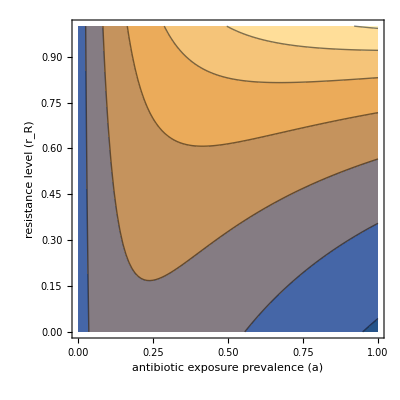

```mathematica
ListContourPlot[Flatten[R0eval,1], FrameLabel->{"antibiotic exposure prevalence (a)", "resistance level (r_R)"}]
```

## microbiome competition (2 strain, exclusive colonization)

```mathematica
Remove["Global`*"]
```

### assumptions

#### acquisition

```mathematica
Subscript[λ, Sϵ]=(1-ϵ)β (Subscript[X, Se]+Subscript[X, Sd]); 
Subscript[λ, S]=β (Subscript[X, Sd]+Subscript[X, Se]);
Subscript[λ, Rϵ]=(1-ϵ)β(Subscript[X, Re]+Subscript[X, Rd]);
Subscript[λ, R]=β(Subscript[X, Rd]+Subscript[X, Re]);
Subscript[α, S]=Subscript[αα, S](1-a(1-Subscript[r, S]));
Subscript[α, Sϕ]=ϕ Subscript[αα, S](1-a(1-Subscript[r, S]));
Subscript[α, R]=Subscript[αα, R](1-a(1-Subscript[r, R]));
Subscript[α, Rϕ]=ϕ Subscript[αα, R](1-a(1-Subscript[r, R]));
```

#### fitness costs of resistance

```mathematica
Subscript[γ, S]=γγ ;
Subscript[γ, Sη]=(1-η)γγ ;
Subscript[γ, R]=γγ(1+c) ;
Subscript[γ, Rη]=(1-η)γγ (1+c);
```

#### antibiotics

```mathematica
Subscript[σ, S]=a(1-Subscript[r, S])Subscript[θ, X];
Subscript[σ, R]=a(1-Subscript[r, R])Subscript[θ, X];
Subscript[σ, m]=a Subscript[θ, m];
```

#### microbiome recovery

```mathematica
δ=δδ(1-a);
```

### ODEs

```mathematica
Subscript[dS, e] = (1-Subscript[f, X])(1-Subscript[f, d])μ-Subscript[S, e](Subscript[λ, Sϵ]+Subscript[λ, Rϵ]+Subscript[α, S]+Subscript[α, R]+Subscript[σ, m]+μ)+Subscript[S, d] δ+Subscript[X, Se](Subscript[γ, S]+Subscript[σ, S])+Subscript[X, Re](Subscript[γ, R]+Subscript[σ, R]);
Subscript[dS, d]=(1-Subscript[f, X])Subscript[f, d] μ+Subscript[S, e] Subscript[σ, m]-Subscript[S, d](Subscript[λ, S]+Subscript[λ, R]+Subscript[α, Sϕ]+Subscript[α, Rϕ]+δ+μ)+Subscript[X, Sd](Subscript[γ, Sη]+Subscript[σ, S])+Subscript[X, Rd](Subscript[γ, Rη]+Subscript[σ, R]);
Subscript[dX, Se] =  Subscript[f, X](1-Subscript[f, R])(1-Subscript[f, d]) μ+Subscript[S, e](Subscript[λ, Sϵ]+Subscript[α, S])+Subscript[X, Sd] δ-Subscript[X, Se](Subscript[γ, S]+Subscript[σ, S]+Subscript[σ, m]+μ);
Subscript[dX, Sd] =  Subscript[f, X](1-Subscript[f, R])Subscript[f, d] μ+Subscript[S, d](Subscript[λ, S]+Subscript[α, Sϕ])+Subscript[X, Se] Subscript[σ, m]-Subscript[X, Sd](δ+Subscript[γ, Sη]+Subscript[σ, S]+μ);
Subscript[dX, Re] =  Subscript[f, X] Subscript[f, R](1-Subscript[f, d]) μ+Subscript[S, e](Subscript[λ, Rϵ]+Subscript[α, R])-Subscript[X, Re](Subscript[γ, R]+Subscript[σ, R]+Subscript[σ, m]+μ)+Subscript[X, Rd] δ;
Subscript[dX, Rd] =  Subscript[f, X] Subscript[f, R] Subscript[f, d] μ+Subscript[S, d](Subscript[λ, R]+Subscript[α, Rϕ])+Subscript[X, Re] Subscript[σ, m]-Subscript[X, Rd](δ+Subscript[γ, Rη]+Subscript[σ, R]+μ);
```

### parameter values

```mathematica
paramsMicrobiome2strain = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,
Subscript[r, S]->0,Subscript[θ, X]->0.2,Subscript[θ, m]->1,
δδ->1/7,ϵ->0.5,η->0.5,ϕ->5
};
```

```mathematica
paramsMicrobiome2strainNoR = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0,γγ->0.03,c->0,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0,
Subscript[r, S]->0,Subscript[θ, X]->0.2,Subscript[θ, m]->1,
δδ->1/7,ϵ->0.5,η->0.5,ϕ->5
};
```

### R_0

#### NGM

```mathematica
F={{(Subscript[α, R]+(1-ϵ)β)Subscript[S, eDFE],(Subscript[α, R]+(1-ϵ)β)Subscript[S, eDFE]},{(Subscript[α, R] ϕ+β)Subscript[S, dDFE],(Subscript[α, R] ϕ+β)Subscript[S, dDFE]}};
V={{Subscript[γ, R]+Subscript[σ, R]+Subscript[σ, m]+μ, -δ},{-Subscript[σ, m],δ+(1-η)Subscript[γ, R]+Subscript[σ, R]+μ}};
NGM = F.Inverse[V];
R0=Total[Eigenvalues[NGM]];
R0//FullSimplify
```

(S_dDFE (β+ϕ (1-a+a r_R) αα_R) (γγ+c γγ+δδ-a δδ+μ+a θ_m-a (-1+r_R) θ_X)+S_eDFE (β (-1+ϵ)+(-1+a-a r_R) αα_R) ((-1+a) δδ+(1+c) γγ (-1+η)-μ-a θ_m+a (-1+r_R) θ_X))/(-((-1+a) δδ+(1+c) γγ (-1+η)-μ+a (-1+r_R) θ_X) (γγ+c γγ+μ+(a-a r_R) θ_X)+a θ_m (-(1+c) γγ (-1+η)+μ+(a-a r_R) θ_X))

#### numerical evaluation

```mathematica
(*function to select equilibrium values of Subscript[S, e] and Subscript[S, d] from solution*)
```

```mathematica
f[sol_]:={Subscript[S, e]/.sol[[1,1]],Subscript[S, d]/.sol[[1,2]]}
```

```mathematica
R0eval=Table[{a,Subscript[r, R],R0/.paramsMicrobiome2strain/.Thread[{Subscript[S, eDFE],Subscript[S, dDFE]}->f[NSolve[{Subscript[dS, e]==0,Subscript[dS, d]==0,Subscript[dX, Se]==0,Subscript[dX, Sd]==0, Subscript[dX, Re]==0,Subscript[dX, Rd]==0,0≤Subscript[S, e]≤1,0≤Subscript[S, d]≤1,0≤Subscript[X, Se]≤1,0≤Subscript[X, Sd]≤1,Subscript[X, Re]==0,Subscript[X, Rd]==0}/.paramsMicrobiome2strainNoR,{Subscript[S, e],Subscript[S, d],Subscript[X, Se],Subscript[X, Sd],Subscript[X, Re],Subscript[X, Rd]}]]]},{a,0,1,0.02},{Subscript[r, R],0,1,0.02}];
```

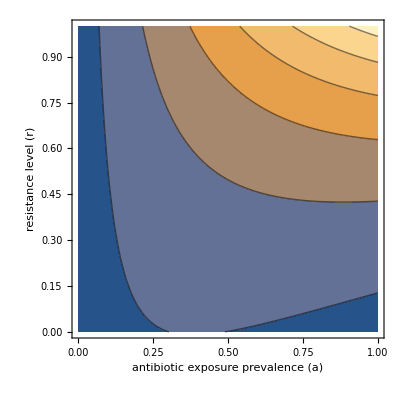

```mathematica
ListContourPlot[Flatten[R0eval,1], FrameLabel->{"antibiotic exposure prevalence (a)", "resistance level (r)"}]
```

## microbiome competition (2 strain, exclusive colonization, horizontal gene transfer)

```mathematica
Remove["Global`*"]
```

### assumptions

#### acquisition

```mathematica
Subscript[λ, Sϵ]=(1-ϵ)β (Subscript[X, Ses]+Subscript[X, Ser]+Subscript[X, Sds]+Subscript[X, Sdr]); 
Subscript[λ, S]=β (Subscript[X, Ses]+Subscript[X, Ser]+Subscript[X, Sds]+Subscript[X, Sdr]);
Subscript[λ, Rϵ]=(1-ϵ)β(Subscript[X, Res]+Subscript[X, Rer]+Subscript[X, Rds]+Subscript[X, Rdr]);
Subscript[λ, R]=β(Subscript[X, Res]+Subscript[X, Rer]+Subscript[X, Rds]+Subscript[X, Rdr]);
Subscript[α, S]=Subscript[αα, S](1-a(1-Subscript[r, S]));
Subscript[α, Sϕ]=ϕ Subscript[αα, S](1-a(1-Subscript[r, S]));
Subscript[α, R]=Subscript[αα, R](1-a(1-Subscript[r, R]));
Subscript[α, Rϕ]=ϕ Subscript[αα, R](1-a(1-Subscript[r, R]));
```

#### fitness costs of resistance

```mathematica
Subscript[γ, S]=γγ ;
Subscript[γ, Sη]=(1-η)γγ ;
Subscript[γ, R]=γγ(1+c) ;
Subscript[γ, Rη]=(1-η)γγ (1+c);
```

#### antibiotics

```mathematica
Subscript[σ, S]=a(1-Subscript[r, S])Subscript[θ, X];
Subscript[σ, R]=a(1-Subscript[r, R])Subscript[θ, X];
Subscript[σ, m]=a Subscript[θ, m];
```

#### microbiome recovery

```mathematica
δ=δδ(1-a);
```

### ODEs

#### baseline

```mathematica
Subscript[dS, es] = (1-Subscript[f, X])(1-Subscript[f, d])(1-Subscript[f, ω])μ-Subscript[S, es](Subscript[λ, Sϵ]+Subscript[λ, Rϵ]+Subscript[α, S]+Subscript[α, R]+Subscript[σ, m]+μ)+Subscript[S, ds] δ+Subscript[X, Ses](Subscript[γ, S]+Subscript[σ, S])+Subscript[X, Res](Subscript[γ, R]+Subscript[σ, R]);
Subscript[dS, er] = (1-Subscript[f, X])(1-Subscript[f, d])Subscript[f, ω] μ-Subscript[S, er](Subscript[λ, Sϵ]+Subscript[λ, Rϵ]+Subscript[α, S]+Subscript[α, R]+Subscript[σ, m]+μ)+Subscript[S, dr] δ+Subscript[X, Ser](Subscript[γ, S]+Subscript[σ, S])+Subscript[X, Rer](Subscript[γ, R]+Subscript[σ, R]);
Subscript[dS, ds]=(1-Subscript[f, X])Subscript[f, d](1-Subscript[f, ω])μ+Subscript[S, es](1-ω)Subscript[σ, m]-Subscript[S, ds](Subscript[λ, S]+Subscript[λ, R]+Subscript[α, Sϕ]+Subscript[α, Rϕ]+δ+μ)+Subscript[X, Sds](Subscript[γ, Sη]+Subscript[σ, S])+Subscript[X, Rds](Subscript[γ, Rη]+Subscript[σ, R]);
Subscript[dS, dr]=(1-Subscript[f, X])Subscript[f, d] Subscript[f, ω] μ+Subscript[S, es] ω Subscript[σ, m]+Subscript[S, er] Subscript[σ, m]-Subscript[S, dr](Subscript[λ, S]+Subscript[λ, R]+Subscript[α, Sϕ]+Subscript[α, Rϕ]+δ+μ)+Subscript[X, Sdr](Subscript[γ, Sη]+Subscript[σ, S])+Subscript[X, Rdr](Subscript[γ, Rη]+Subscript[σ, R]);
Subscript[dX, Ses] =  Subscript[f, X](1-Subscript[f, R])(1-Subscript[f, d])(1-Subscript[f, ω]) μ+Subscript[S, es](Subscript[λ, Sϵ]+Subscript[α, S])-Subscript[X, Ses](Subscript[γ, S]+Subscript[σ, S]+Subscript[σ, m]+μ)+Subscript[X, Sds] δ;
Subscript[dX, Ser] =  Subscript[f, X](1-Subscript[f, R])(1-Subscript[f, d]) Subscript[f, ω] μ+Subscript[S, er](Subscript[λ, Sϵ]+Subscript[α, S])-Subscript[X, Ser](Subscript[γ, S]+Subscript[σ, S]+Subscript[σ, m]+μ+Subscript[χ, e])+Subscript[X, Sdr] δ;
Subscript[dX, Sds] =  Subscript[f, X](1-Subscript[f, R])Subscript[f, d](1-Subscript[f, ω]) μ+Subscript[S, ds](Subscript[λ, S]+Subscript[α, Sϕ])+Subscript[X, Ses](1-ω)Subscript[σ, m]-Subscript[X, Sds](Subscript[γ, Sη]+Subscript[σ, S]+δ+μ);
Subscript[dX, Sdr] =  Subscript[f, X](1-Subscript[f, R])Subscript[f, d] Subscript[f, ω] μ+Subscript[S, dr](Subscript[λ, S]+Subscript[α, Sϕ])+Subscript[X, Ses] ω Subscript[σ, m]+Subscript[X, Ser] Subscript[σ, m]-Subscript[X, Sdr](Subscript[γ, Sη]+Subscript[σ, S]+δ+Subscript[χ, d]+μ);
Subscript[dX, Res] =  Subscript[f, X] Subscript[f, R](1-Subscript[f, d]) (1-Subscript[f, ω])μ+Subscript[S, es](Subscript[λ, Rϵ]+Subscript[α, R])-Subscript[X, Res](Subscript[γ, R]+Subscript[σ, R]+Subscript[σ, m]+Subscript[χ, e]+μ)+Subscript[X, Rds] δ;
Subscript[dX, Rer] =  Subscript[f, X] Subscript[f, R](1-Subscript[f, d]) Subscript[f, ω] μ+Subscript[S, er](Subscript[λ, Rϵ]+Subscript[α, R])+Subscript[X, Ser] Subscript[χ, e]+Subscript[X, Res] Subscript[χ, e]-Subscript[X, Rer](Subscript[γ, R]+Subscript[σ, R]+Subscript[σ, m]+μ)+Subscript[X, Rdr] δ;
Subscript[dX, Rds] =  Subscript[f, X] Subscript[f, R] Subscript[f, d](1-Subscript[f, ω]) μ+Subscript[S, ds](Subscript[λ, R]+Subscript[α, Rϕ])+Subscript[X, Res](1-ω)Subscript[σ, m]-Subscript[X, Rds](Subscript[γ, Rη]+Subscript[σ, R]+δ+Subscript[χ, d]+μ);
Subscript[dX, Rdr] =  Subscript[f, X] Subscript[f, R] Subscript[f, d] Subscript[f, ω] μ+Subscript[S, dr](Subscript[λ, R]+Subscript[α, Rϕ])+Subscript[X, Sdr] Subscript[χ, d]+Subscript[X, Res] ω Subscript[σ, m]+Subscript[X, Rer] Subscript[σ, m]+Subscript[X, Rds] Subscript[χ, d]-Subscript[X, Rdr](Subscript[γ, Rη]+Subscript[σ, R]+δ+μ);
```

### parameter values

```mathematica
paramsHGTnoInteractionsχnone = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, ω]->0,
Subscript[r, S]->0,Subscript[r, R]->0.4,Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7,
ϵ->0,η->0,ϕ->1,Subscript[χ, e]->0,Subscript[χ, d]->0,ω->0
};
paramsHGTnoInteractionsχlow = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, ω]->0,
Subscript[r, S]->0,Subscript[r, R]->0.4,Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7,
ϵ->0,η->0,ϕ->1,Subscript[χ, e]->0.01,Subscript[χ, d]->0.1,ω->0
};
paramsHGTnoInteractionsχhigh = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, ω]->0,
Subscript[r, S]->0,Subscript[r, R]->0.4,Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7,
ϵ->0,η->0,ϕ->1,Subscript[χ, e]->0.1,Subscript[χ, d]->1,ω->0
};
paramsHGTwithInteractionsχnone = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, ω]->0,
Subscript[r, S]->0,Subscript[r, R]->0.4,Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7,
ϵ->0.5,η->0.5,ϕ->5,Subscript[χ, e]->0,Subscript[χ, d]->0,ω->0
};
paramsHGTwithInteractionsχlow = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, ω]->0,
Subscript[r, S]->0,Subscript[r, R]->0.4,Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7,
ϵ->0.5,η->0.5,ϕ->5,Subscript[χ, e]->0.01,Subscript[χ, d]->0.1,ω->0
};
paramsHGTwithInteractionsχhigh = {
β->0.2,Subscript[αα, S]->0.01,Subscript[αα, R]->0.01,γγ->0.03,c->1,
μ->0.1,Subscript[f, d]->0,Subscript[f, X]->0.1,Subscript[f, R]->0.5,Subscript[f, ω]->0,
Subscript[r, S]->0,Subscript[r, R]->0.4,Subscript[θ, X]->0.2,Subscript[θ, m]->1,δδ->1/7,
ϵ->0.5,η->0.5,ϕ->5,Subscript[χ, e]->0.1,Subscript[χ, d]->1,ω->0
};
```

### prevalence

#### evaluated for a ∈ {0,1}, for models with and without microbiome-pathogen competition, and with and without HGT

```mathematica
solsHGTnoInteractionsχnone=Table[Flatten[{a,DeleteDuplicates[Round[{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]}/.NSolve[{Subscript[dS, es]==0,Subscript[dS, er]==0,Subscript[dS, ds]==0,Subscript[dS, dr]==0,Subscript[dX, Ses]==0,Subscript[dX, Ser]==0,Subscript[dX, Sds]==0,Subscript[dX, Sdr]==0,Subscript[dX, Res]==0,Subscript[dX, Rer]==0,Subscript[dX, Rds]==0,Subscript[dX, Rdr]==0,0≤Subscript[S, es]≤1,0≤Subscript[S, er]≤1,0≤Subscript[S, ds]≤1,0≤Subscript[S, dr]≤1,0≤Subscript[X, Ses]≤1,0≤Subscript[X, Ser]≤1,0≤Subscript[X, Sds]≤1,0≤Subscript[X, Sdr]≤1,0≤Subscript[X, Res]≤1,0≤Subscript[X, Rer]≤1,0≤Subscript[X, Rds]≤1,0≤Subscript[X, Rdr]≤1}/.paramsHGTnoInteractionsχnone/.{a->a},{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]},Reals],0.001]]}],{a,0,1,0.1}];
```

$Aborted

```mathematica
solsHGTnoInteractionsχlow=Table[Flatten[{a,DeleteDuplicates[Round[{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]}/.NSolve[{Subscript[dS, es]==0,Subscript[dS, er]==0,Subscript[dS, ds]==0,Subscript[dS, dr]==0,Subscript[dX, Ses]==0,Subscript[dX, Ser]==0,Subscript[dX, Sds]==0,Subscript[dX, Sdr]==0,Subscript[dX, Res]==0,Subscript[dX, Rer]==0,Subscript[dX, Rds]==0,Subscript[dX, Rdr]==0,0≤Subscript[S, es]≤1,0≤Subscript[S, er]≤1,0≤Subscript[S, ds]≤1,0≤Subscript[S, dr]≤1,0≤Subscript[X, Ses]≤1,0≤Subscript[X, Ser]≤1,0≤Subscript[X, Sds]≤1,0≤Subscript[X, Sdr]≤1,0≤Subscript[X, Res]≤1,0≤Subscript[X, Rer]≤1,0≤Subscript[X, Rds]≤1,0≤Subscript[X, Rdr]≤1}/.paramsHGTnoInteractionsχlow/.{a->a},{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]},Reals],0.001]]}],{a,0,1,0.1}];
```

```mathematica
solsHGTnoInteractionsχhigh=Table[Flatten[{a,DeleteDuplicates[Round[{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]}/.NSolve[{Subscript[dS, es]==0,Subscript[dS, er]==0,Subscript[dS, ds]==0,Subscript[dS, dr]==0,Subscript[dX, Ses]==0,Subscript[dX, Ser]==0,Subscript[dX, Sds]==0,Subscript[dX, Sdr]==0,Subscript[dX, Res]==0,Subscript[dX, Rer]==0,Subscript[dX, Rds]==0,Subscript[dX, Rdr]==0,0≤Subscript[S, es]≤1,0≤Subscript[S, er]≤1,0≤Subscript[S, ds]≤1,0≤Subscript[S, dr]≤1,0≤Subscript[X, Ses]≤1,0≤Subscript[X, Ser]≤1,0≤Subscript[X, Sds]≤1,0≤Subscript[X, Sdr]≤1,0≤Subscript[X, Res]≤1,0≤Subscript[X, Rer]≤1,0≤Subscript[X, Rds]≤1,0≤Subscript[X, Rdr]≤1}/.paramsHGTnoInteractionsχhigh/.{a->a},{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]},Reals],0.001]]}],{a,0,1,0.1}];
```

```mathematica
solsHGTwithInteractionsχnone=Table[Flatten[{a,DeleteDuplicates[Round[{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]}/.NSolve[{Subscript[dS, es]==0,Subscript[dS, er]==0,Subscript[dS, ds]==0,Subscript[dS, dr]==0,Subscript[dX, Ses]==0,Subscript[dX, Ser]==0,Subscript[dX, Sds]==0,Subscript[dX, Sdr]==0,Subscript[dX, Res]==0,Subscript[dX, Rer]==0,Subscript[dX, Rds]==0,Subscript[dX, Rdr]==0,0≤Subscript[S, es]≤1,0≤Subscript[S, er]≤1,0≤Subscript[S, ds]≤1,0≤Subscript[S, dr]≤1,0≤Subscript[X, Ses]≤1,0≤Subscript[X, Ser]≤1,0≤Subscript[X, Sds]≤1,0≤Subscript[X, Sdr]≤1,0≤Subscript[X, Res]≤1,0≤Subscript[X, Rer]≤1,0≤Subscript[X, Rds]≤1,0≤Subscript[X, Rdr]≤1}/.paramsHGTwithInteractionsχnone/.{a->a},{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]},Reals],0.001]]}],{a,0,1,0.1}];
```

```mathematica
solsHGTwithInteractionsχlow=Table[Flatten[{a,DeleteDuplicates[Round[{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]}/.NSolve[{Subscript[dS, es]==0,Subscript[dS, er]==0,Subscript[dS, ds]==0,Subscript[dS, dr]==0,Subscript[dX, Ses]==0,Subscript[dX, Ser]==0,Subscript[dX, Sds]==0,Subscript[dX, Sdr]==0,Subscript[dX, Res]==0,Subscript[dX, Rer]==0,Subscript[dX, Rds]==0,Subscript[dX, Rdr]==0,0≤Subscript[S, es]≤1,0≤Subscript[S, er]≤1,0≤Subscript[S, ds]≤1,0≤Subscript[S, dr]≤1,0≤Subscript[X, Ses]≤1,0≤Subscript[X, Ser]≤1,0≤Subscript[X, Sds]≤1,0≤Subscript[X, Sdr]≤1,0≤Subscript[X, Res]≤1,0≤Subscript[X, Rer]≤1,0≤Subscript[X, Rds]≤1,0≤Subscript[X, Rdr]≤1}/.paramsHGTwithInteractionsχlow/.{a->a},{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]},Reals],0.001]]}],{a,0,1,0.1}];
```

```mathematica
solsHGTwithInteractionsχhigh=Table[Flatten[{a,DeleteDuplicates[Round[{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]}/.NSolve[{Subscript[dS, es]==0,Subscript[dS, er]==0,Subscript[dS, ds]==0,Subscript[dS, dr]==0,Subscript[dX, Ses]==0,Subscript[dX, Ser]==0,Subscript[dX, Sds]==0,Subscript[dX, Sdr]==0,Subscript[dX, Res]==0,Subscript[dX, Rer]==0,Subscript[dX, Rds]==0,Subscript[dX, Rdr]==0,0≤Subscript[S, es]≤1,0≤Subscript[S, er]≤1,0≤Subscript[S, ds]≤1,0≤Subscript[S, dr]≤1,0≤Subscript[X, Ses]≤1,0≤Subscript[X, Ser]≤1,0≤Subscript[X, Sds]≤1,0≤Subscript[X, Sdr]≤1,0≤Subscript[X, Res]≤1,0≤Subscript[X, Rer]≤1,0≤Subscript[X, Rds]≤1,0≤Subscript[X, Rdr]≤1}/.paramsHGTwithInteractionsχhigh/.{a->a},{Subscript[S, es],Subscript[S, er],Subscript[S, ds],Subscript[S, dr],Subscript[X, Ses],Subscript[X, Ser],Subscript[X, Sds],Subscript[X, Sdr],Subscript[X, Res],Subscript[X, Rer],Subscript[X, Rds],Subscript[X, Rdr]},Reals],0.001]]}],{a,0,1,0.1}];
```

```mathematica
prevalenceHGTnoInteractionsχnone=Transpose[{solsHGTnoInteractionsχnone[[All,1]],solsHGTnoInteractionsχnone[[All,10]]+solsHGTnoInteractionsχnone[[All,11]]+solsHGTnoInteractionsχnone[[All,12]]+solsHGTnoInteractionsχnone[[All,13]]}];
prevalenceHGTnoInteractionsχlow=Transpose[{solsHGTnoInteractionsχlow[[All,1]],solsHGTnoInteractionsχlow[[All,10]]+solsHGTnoInteractionsχlow[[All,11]]+solsHGTnoInteractionsχlow[[All,12]]+solsHGTnoInteractionsχlow[[All,13]]}];
prevalenceHGTnoInteractionsχhigh=Transpose[{solsHGTnoInteractionsχhigh[[All,1]],solsHGTnoInteractionsχhigh[[All,10]]+solsHGTnoInteractionsχhigh[[All,11]]+solsHGTnoInteractionsχhigh[[All,12]]+solsHGTnoInteractionsχhigh[[All,13]]}];
prevalenceHGTwithInteractionsχnone=Transpose[{solsHGTwithInteractionsχnone[[All,1]],solsHGTwithInteractionsχnone[[All,10]]+solsHGTwithInteractionsχnone[[All,11]]+solsHGTwithInteractionsχnone[[All,12]]+solsHGTwithInteractionsχnone[[All,13]]}];
prevalenceHGTwithInteractionsχlow=Transpose[{solsHGTwithInteractionsχlow[[All,1]],solsHGTwithInteractionsχlow[[All,10]]+solsHGTwithInteractionsχlow[[All,11]]+solsHGTwithInteractionsχlow[[All,12]]+solsHGTwithInteractionsχlow[[All,13]]}];
prevalenceHGTwithInteractionsχhigh=Transpose[{solsHGTwithInteractionsχhigh[[All,1]],solsHGTwithInteractionsχhigh[[All,10]]+solsHGTwithInteractionsχhigh[[All,11]]+solsHGTwithInteractionsχhigh[[All,12]]+solsHGTwithInteractionsχhigh[[All,13]]}];
```

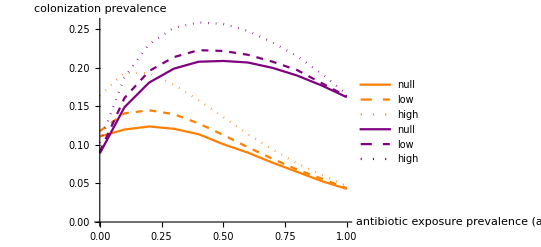

```mathematica
ListLinePlot[{prevalenceHGTnoInteractionsχnone,prevalenceHGTnoInteractionsχlow,prevalenceHGTnoInteractionsχhigh,
prevalenceHGTwithInteractionsχnone,prevalenceHGTwithInteractionsχlow,prevalenceHGTwithInteractionsχhigh},PlotLegends->{"null","low","high","null","low","high"},AxesLabel->{"antibiotic exposure prevalence (a)", "colonization prevalence"},PlotStyle->{{Orange}, {Orange,Dashed}, {Orange,Dotted}, Purple, {Purple,Dashed}, {Purple,Dotted}}]
```